```mathematica
a=Import["~/ACS_LOG_2025-02-26_H12_M22_S01-2025-03-07/ACS_LOG_2025-02-26_H12_M22_S01.csv","CSV"];
```

```mathematica
a[[Length[a]]]
```

{2025 Mar 07 14:44:48.704,786167.,200678.,23.625,0.,0.,22.125,21.875,-14.625,-4.6875,22.375,-7.25,36.25,1}

```mathematica
a[[1]]
```

{2025 Feb 26 12:22:01.489,0.01,200437.,22.6875,0.,0.,21.125,20.875,-15.,20.9375,20.875,15.8125,19.0625,0}

```mathematica
Length[a[[1]]]
```

14

```mathematica
a[[Length[a]]]
```

{2025 Mar 07 14:44:48.704,786167.,200678.,23.625,0.,0.,22.125,21.875,-14.625,-4.6875,22.375,-7.25,36.25,1}

```mathematica
a[[1,2]]
```

0.01

```mathematica
a[[1,9]]
```

-15.

```mathematica
a[[Length[a],9]]
```

-14.625

```mathematica
redline={{a[[1,2]],0},{a[[Length[a],2]],0}}
```

{{0.01,0},{786167.,0}}

```mathematica
greenline={{a[[1,2]],-15},{a[[Length[a],2]],-15}}
```

{{0.01,-15},{786167.,-15}}

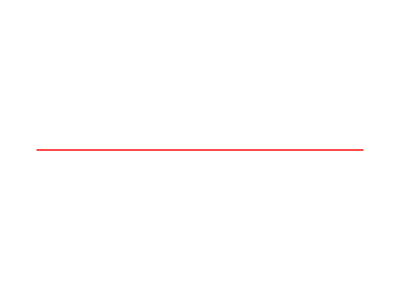

```mathematica
RedLine=Show[Graphics[{Hue[1],Line[redline]}]]
```

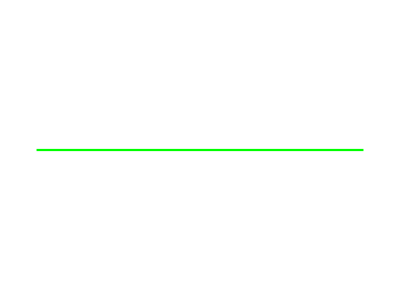

```mathematica
GreenLine=Show[Graphics[{Thickness[0.004],Green,Line[greenline]}]]
```

```mathematica
b=Transpose[a];
```

```mathematica
c1=Table[{b[[2,i]],b[[9,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g1=ListPlot[c1,ImageSize->1000,PlotRange->{-20,0},Axes->False,Frame->True];
```

```mathematica
Show[g1,RedLine,GreenLine]
```

-Graphics-

```mathematica
c2=Table[{b[[2,i]],b[[10,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g2=ListPlot[c2,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
Show[g2,RedLine]
```

-Graphics-

```mathematica
c4=Table[{b[[2,i]],b[[12,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g4=ListPlot[c4,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
Show[g4,RedLine]
```

-Graphics-

```mathematica
c5=Table[{b[[2,i]],b[[13,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g5=ListPlot[c5,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
Show[g5,RedLine]
```

-Graphics-